```mathematica
SetDirectory[NotebookDirectory[]]
rasterizeBackground[g_,res_: 100]:=Show[Graphics[{Inset[Rasterize[Show[g,ImagePadding->0,ImageMargins->0,LabelStyle->Opacity[0],FrameTicksStyle->Opacity[0],FrameStyle->Opacity[0],AxesStyle->Opacity[0],TicksStyle->Opacity[0],PlotRangeClipping->False],ImageResolution->res],Scaled[{0,0}],Scaled[{0,0}],Scaled[1]]}],Sequence@@Options[g],Sequence@@Options[g,PlotRange],Sequence@@Options[g,Epilog]];
```

/home/zack/oscillators/faraday

Single run plots

```mathematica
filebase="data/cylindersaturate4";
lst=StringSplit[Import[filebase<>".txt"],"\n"];
meshpoints=ToExpression[lst[[FirstPosition[lst,"Mesh points"][[1]]+1]]];
mesh=Partition[Partition[BinaryReadList[filebase<>".npy","Real64"][[1+(10+BinaryReadList[filebase<>".npy","Integer16"][[5]])*8/64;;-1]],3],meshpoints];
norms=BinaryReadList[filebase<>"norms.npy","Real64"][[1+(10+BinaryReadList[filebase<>"norms.npy","Integer16"][[5]])*8/64;;-1]];
height=First@ToExpression[StringSplit[lst[[FirstPosition[lst,"Height"][[1]]+1]]]];
radius=First@ToExpression[StringSplit[lst[[FirstPosition[lst,"Radius"][[1]]+1]]]];
steps=First@ToExpression[StringSplit[lst[[FirstPosition[lst,"Steps"][[1]]+1]]]];
acc=ToExpression[StringSplit[lst[[-1]]," "]][[2]];
freq=ToExpression[StringSplit[lst[[-1]]," "]][[1]];
amp=980*acc/(2*Pi*freq)^2;
z0=amp*Sin[2*Pi*m/15];
lst[[1]]
{radius,height}
top=1+ToExpression[StringSplit[lst[[FirstPosition[lst,"Surface points coordinates"][[1]]+1]]]];
top2=1+ToExpression[StringSplit[lst[[FirstPosition[lst,"Interior surface points coordinates"][[1]]+1]]]];
bottom=1+ToExpression[StringSplit[lst[[FirstPosition[lst,"Substrate points coordinates"][[1]]+1]]]];
con=Partition[1+ToExpression[StringSplit[lst[[FirstPosition[lst,"Mesh cells"][[1]]+1]]," "]],4];
contop=Cases[con,u_/;Length[Intersection[top,u]]==3];
conbottom=Cases[con,u_/;Length[Intersection[bottom,u]]==3];
sides=Flatten[Position[mesh[[-1]],u_/;Length[u]>0&&Abs[(u[[1]]^2+u[[2]]^2)^(1/2)-radius]<0.1]];
consides=Cases[con,u_/;Length[Intersection[sides,u]]==3];
m=Length[mesh]-5;
mesh2=mesh[[m]];
p0=ListPlot[Transpose[{Range[Length[norms]]/steps/freq,Log[norms]/Log[10]}],Joined->True,PlotRange->All,ImageSize->350,ImagePadding->{{75,15},{75,15}},AspectRatio->1,Axes->False,Frame->True,FrameLabel->{"Time(s)",Log[Abs[DisplayForm[RowBox[{H,"/(2cm)"}]]]]},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2.0]],PlotStyle->Directive[LightGray,AbsoluteThickness[1]],FrameStyle->Directive[Black,AbsoluteThickness[2.0]]];
p=Grid[{{Show[p0,ListPlot[Transpose[{Range[m]/steps/freq,Log[norms[[1;;m]]]/Log[10]}],Joined->True,PlotStyle->Directive[Black,AbsoluteThickness[2]]]],Show[ListDensityPlot[mesh2[[top]],PlotRange->All,InterpolationOrder->10,ImageSize->350,ImagePadding->{{75,15},{75,15}},AspectRatio->1,Axes->False,Frame->True,FrameLabel->{"x(cm)","y(cm)"},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2.0]]],Graphics[Line[{mesh2[[#[[1]],{1,2}]],mesh2[[#[[2]],{1,2}]]}]&/@DeleteDuplicates[Flatten[Subsets[#,{2}]&/@(Intersection[#,top]&/@contop),1]]],ListPlot[{mesh2[[Complement[top,top2],{1,2}]],mesh2[[top2,{1,2}]]},PlotStyle->{Directive[Black,PointSize[0.02]],Directive[LightGray,PointSize[0.02]]}]],Rasterize[Show[Graphics3D[{Sphere[#,0.03]&/@mesh2[[top]],Sphere[#,0.03]&/@mesh2[[bottom]],Sphere[#,0.03]&/@mesh2[[sides]],Opacity[0.5],EdgeForm[Directive[Black,Opacity[0.5]]],FaceForm[Blue],Triangle[{mesh2[[#[[1]]]],mesh2[[#[[2]]]],mesh2[[#[[3]]]]}]&/@(Intersection[#,sides]&/@consides),Thickness[0.001],Opacity[0.5],Line[{mesh2[[#[[1]]]],mesh2[[#[[2]]]]}]&/@Subsets[#,{2}]&/@(Intersection[#,top]&/@contop),Line[{mesh2[[#[[1]]]],mesh2[[#[[2]]]]}]&/@Subsets[#,{2}]&/@(Intersection[#,bottom]&/@conbottom)},Boxed->False,ImageSize->500,PlotRange->{All,All,{Min[mesh[[All,All,3]]]-1,Max[mesh[[All,All,3]]]+1}}],
Show[ListPlot3D[mesh2[[bottom]],PlotRange->{All,All,{Min[mesh[[All,All,3]]]-1,Max[mesh[[All,All,3]]]+1}},Boxed->False,AspectRatio->1,Mesh->None,Axes->False,ImageSize->500,PlotStyle->Opacity[0.5]],ListPlot3D[mesh2[[top]],PlotRange->{All,All,{Min[mesh[[All,All,3]]]-1,Max[mesh[[All,All,3]]]+1}},Boxed->False,AspectRatio->1,Mesh->None,Axes->False,ImageSize->500,PlotStyle->Directive[Opacity[0.5],Blue]]],ViewPoint->{0, -3, 1}],ImageSize->500]}}]
Export["cylindersaturate.pdf",p]
lst[[-1]]
```

./faraday.py --geometry cylinder --xmesh 15 --zmesh 15 --refinement 0 --radius 2 --height 2 --iamp 5e-3 --bmesh 0 --nonlinear 1 --time 300 --filebase data/cylindersaturate4 --contact stick --frequency 24 --acceleration 1.0

{2.,2.}

-Graphics-

cylindersaturate.pdf

24.000000 1.000000 0.499775 0.028554 1.202413

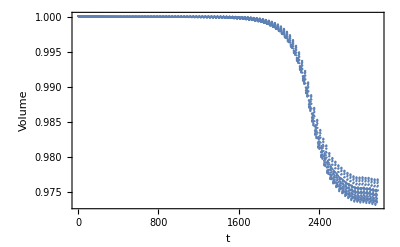

```mathematica
(* Numerical loss of fluid volume during saturation, but not too bad...*)
ListPlot[Total[#[[top,3]]]/(Length[top]*height)&/@mesh,Axes->False,Frame->True,FrameLabel->{t,"Volume"},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]]]
```

```mathematica
radius=2;
modes=Sort[Join[Table[(x/radius/.FindRoot[D[BesselJ[n,x],x],{x,2*BesselJZero[n,1]/3}]),{n,1,5}],Table[N[BesselJZero[n,1]/radius],{n,1,5}],Table[(x/radius/.FindRoot[D[BesselJ[n,x],x],{x,(BesselJZero[n,2]+BesselJZero[n,1])/2}]),{n,0,5}],Table[N[BesselJZero[n,2]/radius],{n,0,5}]]]
frequencies=2*(980*#*Tanh[height*#]*(1+72/980*#^2))^(1/2)/(2*Pi)&/@modes
modes2=Sort[Join[Table[({x/radius,{0,n}}/.FindRoot[D[BesselJ[n,x],x],{x,2*BesselJZero[n,1]/3}]),{n,1,5}],Table[{N[BesselJZero[n,1]/radius],{1/2,n}},{n,1,5}],Table[({x/radius,{1,n}}/.FindRoot[D[BesselJ[n,x],x],{x,(BesselJZero[n,2]+BesselJZero[n,1])/2}]),{n,0,5}],Table[{N[BesselJZero[n,2]/radius],{3/2,n}},{n,0,5}]]]
frequencies2={#[[1]],2*(980*#[[1]]*Tanh[height*#[[1]]]*(1+72/980*#[[1]]^2))^(1/2)/(2*Pi),#[[2]]}&/@modes2
```

{0.920592,1.52712,1.91585,1.91585,2.10059,2.56781,2.65878,2.66572,2.76004,3.19008,3.20781,3.35307,3.50779,3.79417,4.00762,4.20862,4.38574,4.6412,4.88051,5.25993,5.53235,6.1693}

{9.60909,13.2976,15.5341,15.5341,16.6154,19.454,20.0274,20.0715,20.6743,23.5284,23.6499,24.6568,25.7522,27.8424,29.4533,31.0115,32.4174,34.4989,36.5058,39.7984,42.2446,48.2236}

{{0.920592,{0,1}},{1.52712,{0,2}},{1.91585,{1/2,1}},{1.91585,{1,0}},{2.10059,{0,3}},{2.56781,{1/2,2}},{2.65878,{0,4}},{2.66572,{1,1}},{2.76004,{3/2,0}},{3.19008,{1/2,3}},{3.20781,{0,5}},{3.35307,{1,2}},{3.50779,{3/2,1}},{3.79417,{1/2,4}},{4.00762,{1,3}},{4.20862,{3/2,2}},{4.38574,{1/2,5}},{4.6412,{1,4}},{4.88051,{3/2,3}},{5.25993,{1,5}},{5.53235,{3/2,4}},{6.1693,{3/2,5}}}

{{0.920592,9.60909,{0,1}},{1.52712,13.2976,{0,2}},{1.91585,15.5341,{1/2,1}},{1.91585,15.5341,{1,0}},{2.10059,16.6154,{0,3}},{2.56781,19.454,{1/2,2}},{2.65878,20.0274,{0,4}},{2.66572,20.0715,{1,1}},{2.76004,20.6743,{3/2,0}},{3.19008,23.5284,{1/2,3}},{3.20781,23.6499,{0,5}},{3.35307,24.6568,{1,2}},{3.50779,25.7522,{3/2,1}},{3.79417,27.8424,{1/2,4}},{4.00762,29.4533,{1,3}},{4.20862,31.0115,{3/2,2}},{4.38574,32.4174,{1/2,5}},{4.6412,34.4989,{1,4}},{4.88051,36.5058,{3/2,3}},{5.25993,39.7984,{1,5}},{5.53235,42.2446,{3/2,4}},{6.1693,48.2236,{3/2,5}}}

Animation

```mathematica
m0=Length[mesh]-750;
m1=Length[mesh]
If[!DirectoryQ["cylinderanimation"],CreateDirectory["cylinderanimation"]];
Monitor[Do[
mesh2={#[[1]],#[[2]],z0+#[[3]]}&/@mesh[[m]];
z0=amp*Sin[2*Pi*m/steps];
p=Grid[{{Show[p0,ListPlot[Transpose[{Range[m]/steps/freq,Log[norms[[1;;m]]]/Log[10]}],Joined->True,PlotStyle->Directive[Black,AbsoluteThickness[2]]]],Show[ListDensityPlot[mesh2[[top]],PlotRange->All,InterpolationOrder->10,ImageSize->350,ImagePadding->{{75,15},{75,15}},AspectRatio->1,Axes->False,Frame->True,FrameLabel->{"x(cm)","y(cm)"},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2.0]]],Graphics[Line[{mesh2[[#[[1]],{1,2}]],mesh2[[#[[2]],{1,2}]]}]&/@DeleteDuplicates[Flatten[Subsets[#,{2}]&/@(Intersection[#,top]&/@contop),1]]],ListPlot[{mesh2[[Complement[top,top2],{1,2}]],mesh2[[top2,{1,2}]]},PlotStyle->{Directive[Black,PointSize[0.02]],Directive[LightGray,PointSize[0.02]]}]],Show[Graphics3D[{Sphere[#,0.03]&/@mesh2[[top]],Sphere[#,0.03]&/@mesh2[[bottom]],Sphere[#,0.03]&/@mesh2[[sides]],Opacity[0.5],EdgeForm[Directive[Black,Opacity[0.5]]],FaceForm[Blue],Triangle[{mesh2[[#[[1]]]],mesh2[[#[[2]]]],mesh2[[#[[3]]]]}]&/@(Intersection[#,sides]&/@consides),Thickness[0.001],Opacity[0.5],Line[{mesh2[[#[[1]]]],mesh2[[#[[2]]]]}]&/@Subsets[#,{2}]&/@(Intersection[#,top]&/@contop),Line[{mesh2[[#[[1]]]],mesh2[[#[[2]]]]}]&/@Subsets[#,{2}]&/@(Intersection[#,bottom]&/@conbottom)},Boxed->False,ImageSize->500,PlotRange->{All,All,{-1,height+1}}],Show[ListPlot3D[mesh2[[bottom]],PlotRange->{All,All,{-1,height+1}},Boxed->False,AspectRatio->1,Mesh->None,Axes->False,ImageSize->500,PlotStyle->Opacity[0.5]],ListPlot3D[mesh2[[top]],PlotRange->{All,All,{-1,height+1}},Boxed->False,AspectRatio->1,Mesh->None,Axes->False,ImageSize->500,PlotStyle->Directive[Opacity[0.5],Blue]]],ViewPoint->{0, -3, 1}]}}];
Export["cylinderanimation/"<>IntegerString[m-m0,10,4]<>".png",p,ImageResolution->100];,{m,m0,m1}],N[(m-m0)/(m1-m0)]]
```

3079

Sweep plots

sc3

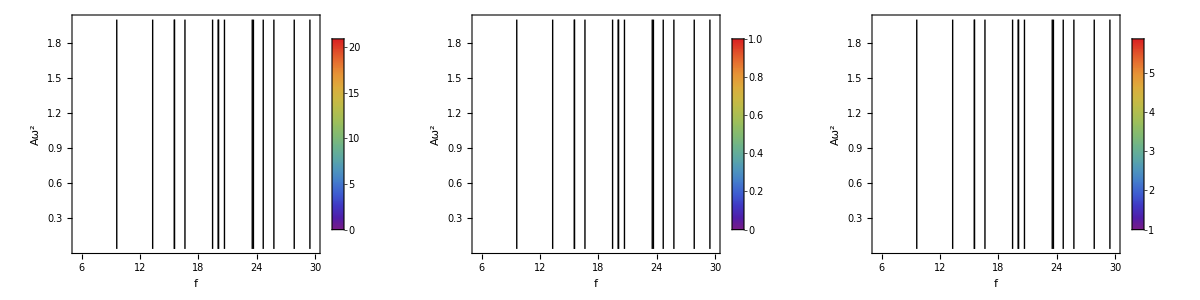

```mathematica
filebase="sc3"
growth1=Flatten[Table[If[FileExistsQ[filebase<>"/params"<>ToString[i]<>".txt"],Internal`StringToDouble/@#&/@DeleteCases[StringSplit/@StringSplit[Import[filebase<>"/params"<>ToString[i]<>".txt"],"\n"],{}],{}],{i,1,50}],1];
Amin=Min[growth1[[All,2]]];
Amax=Max[growth1[[All,2]]];
fmin=Min[growth1[[All,1]]];
fmax=Max[growth1[[All,1]]];
kmin=Min[growth1[[All,5]]];
kmax=Max[growth1[[All,5]]];
max=Max[growth1[[All,4]]];
ν1=2;
ν2=0;
ν3=0.5;
g=980;
σ=72;
p1=Grid[{{Show[rasterizeBackground[Show[ListDensityPlot[growth1[[All,{1,2,4}]],InterpolationOrder->0,PlotRange->{All,All,{0.0,max}},ClippingStyle->None,LabelStyle->Directive[16,Black],ColorFunction->(ColorData["Rainbow"][#/max]&),ColorFunctionScaling->False, FrameLabel->{{Aω^2,None},{f,"Growth Rate"}},Epilog->{Inset[BarLegend[{"Rainbow",{0,max}},LabelStyle->Directive[16,Black]],Scaled[{1.2,0.5}]],Line[{{#,Amin},{#,Amax}}]&/@Cases[frequencies,u_/;u>fmin&&u<fmax]}],Plot[2*(ν1+ν3*k^2+ν2*k*Tanh[k*height])*(1+σ/g*k^2)/(k*Tanh[k*height]*(g+σ*k^2))^(1/2)/.FindRoot[2*Pi*f/2==(k*Tanh[k*height]*(g+σ*k^2))^(1/2), {k,1.0}],{f,fmin,fmax},PlotStyle->Directive[Black]]]],PlotRangeClipping->False,ImageSize->400,ImagePadding->{{65,100},{50,50}}],rasterizeBackground[Show[ListDensityPlot[ReplacePart[growth1[[All,{1,2,3}]],Position[growth1[[All,{1,2,4}]],u_/;u<0]->-1],InterpolationOrder->0,PlotRange->{All,All,{0.0,1.1}},ClippingStyle->None,LabelStyle->Directive[16,Black],ColorFunction->(ColorData["Rainbow"][#/1.0]&),ColorFunctionScaling->False,FrameLabel->{{Aω^2,None},{f,"Frequency"}},ImageSize->300],PlotRangeClipping->None,Epilog->{Inset[BarLegend[{"Rainbow",{0,1}},LabelStyle->Directive[16,Black]],Scaled[{1.2,0.5}]],Line[{{#,Amin},{#,Amax}}]&/@Cases[frequencies,u_/;u>fmin&&u<fmax]},ImageSize->400,ImagePadding->{{65,100},{50,50}}]],rasterizeBackground[Show[ListDensityPlot[ReplacePart[growth1[[All,{1,2,5}]],Position[growth1[[All,{1,2,4}]],u_/;u<0]->-1],InterpolationOrder->0,PlotRange->{All,All,{0.9*kmin,1.1*kmax}},ClippingStyle->None,LabelStyle->Directive[16,Black],ColorFunction->(ColorData["Rainbow"][(#-kmin)/(kmax-kmin)]&),ColorFunctionScaling->False, FrameLabel->{{Aω^2,None},{f,"Wave number"}}],PlotRangeClipping->None,Epilog->{Inset[BarLegend[{"Rainbow",{kmin,kmax}},LabelStyle->Directive[16,Black]],Scaled[{1.2,0.5}]],Line[{{#,Amin},{#,Amax}}]&/@Cases[frequencies,u_/;u>fmin&&u<fmax]},ImageSize->400,ImagePadding->{{65,100},{50,50}}]]}}]
```

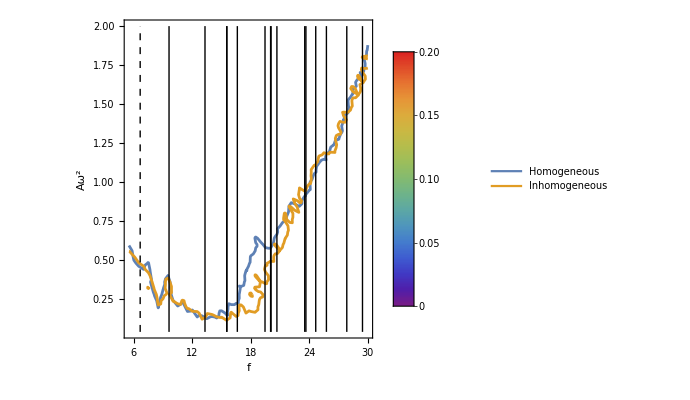

```mathematica
filebase="sc4";
growth2=Flatten[Table[If[FileExistsQ[filebase<>"/params"<>ToString[i]<>".txt"],Internal`StringToDouble/@#&/@DeleteCases[StringSplit/@StringSplit[Import[filebase<>"/params"<>ToString[i]<>".txt"],"\n"],{}],{}],{i,1,50}],1];
sweeps={growth1,growth2};
p=Show@@Table[ListContourPlot[sweeps[[i,All,{1,2,4}]],Contours->{0.0},ContourShading->None,ContourStyle->{Directive[ColorData[97,"ColorList"][[i]],Opacity[1],AbsoluteThickness[2]]},LabelStyle->Directive[16,Black],ColorFunction->(ColorData["Rainbow"][#/max]&),ColorFunctionScaling->False, FrameLabel->{{Aω^2,None},{f,None}},Epilog->{Inset[BarLegend[{"Rainbow",{0,0.2}},LabelStyle->Directive[16,Black]],Scaled[{1.2,0.5}]],AbsoluteThickness[1],Line[{{#,Amin},{#,Amax}}]&/@Cases[frequencies,u_/;u>fmin&&u<fmax],Dashed,Line[{{#,Amin},{#,Amax}}]&/@Cases[frequencies/2,u_/;u>fmin&&u<fmax&&u<Min[frequencies]*0.75]}],{i,1,Length[sweeps]}];
Legended[p,LineLegend[ColorData[97,"ColorList"],{"Homogeneous","Inhomogeneous"}]]
```

Flat substrate Floquet predictions

```mathematica
rate[k_,ω_,A_,ν_]:=Module[{t0,t1,sol,norms,maxes},
t0=2*Pi*25;
t1=2*Pi*50;
sol=First@NDSolve[{ω^2*h''[t]==k*Tanh[k]*((-1+A*ω*Sin[t])*h[t]-ν*ω*h'[t]), h[0]==0.001, h'[0]==0}, h[t], {t,0,t1}];
norms=Table[h[t]/.sol,{t,t0,t1,2*Pi*0.1}];
maxes=First/@Position[Differences[Sign[Differences[norms]]],-2];
If[Mean[Log[Abs[norms]]]/Log[10]<-5,{k,ω,A,1/(0.1*Mean[Differences[maxes]]),-1,norms},{k,ω,A,1/(0.1*Mean[Differences[maxes]]),D[ω*Fit[Transpose[{2*Pi*0.1*maxes,Log[Abs[norms[[maxes]]]]}][[Ceiling[Length[maxes]/2];;-1]],{1,x},x],x],norms}]]
ωmin=1.5;
ωmax=3.0;
Amin=0.0;
Amax=0.3;
ν=0.05;
M=50;
AbsoluteTiming[Monitor[rates=Flatten[Table[First@MaximalBy[Table[rate[k,ω,A,ν][[1;;5]],{k,modes}],#[[5]]&],{ω,ωmin,ωmax,(ωmax-ωmin)/M},{A,Amin,Amax,(Amax-Amin)/M}],1];,N[{(ω-ωmin)/(ωmax-ωmin),(A-Amin)/(Amax-Amin)}]]]
```

{48.6212,Null}

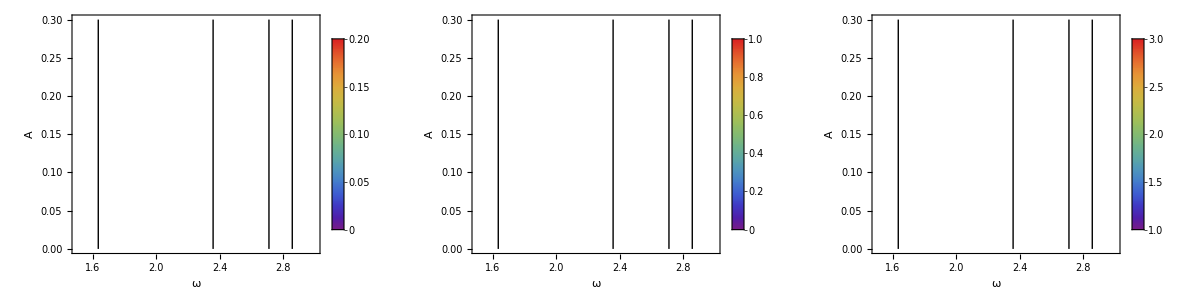

plots/benchmark.pdf

```mathematica
p2=Grid[{{rasterizeBackground[Show[ListDensityPlot[rates[[All,{2,3,5}]],InterpolationOrder->0,ImageSize->300,LabelStyle->Directive[16,Black],PlotRange->{0,0.2},ColorFunctionScaling->False,ColorFunction->(ColorData["Rainbow"][#/0.2]&), FrameLabel->{{A,None},{ω,"Growth Rate"}},ClippingStyle->None],PlotRangeClipping->None,Epilog->{Inset[BarLegend[{"Rainbow",{0,0.2}},LabelStyle->Directive[16,Black]],Scaled[{1.2,0.5}]],Line[{{#,0},{#,0.3}}]&/@Cases[(2*(modes*Tanh[modes])^(1/2)),u_/;u<3]},ImageSize->400,ImagePadding->{{65,100},{50,50}}]],rasterizeBackground[Show[ListDensityPlot[ReplacePart[rates[[All,{2,3,4}]],Position[rates[[All,{2,3,5}]],u_/;u<0]->-1],InterpolationOrder->0,ImageSize->300,LabelStyle->Directive[16,Black],ColorFunctionScaling->False,ColorFunction->(ColorData["Rainbow"][#/1]&),PlotRange->{0,1.1},ClippingStyle->None, FrameLabel->{{A,None},{ω,"Frequency"}}],PlotRangeClipping->None,Epilog->{Inset[BarLegend[{"Rainbow",{0,1}},LabelStyle->Directive[16,Black]],Scaled[{1.2,0.5}]],Line[{{#,0},{#,0.3}}]&/@Cases[(2*(modes*Tanh[modes])^(1/2)),u_/;u<3]},ImageSize->400,ImagePadding->{{65,100},{50,50}}]],rasterizeBackground[Show[ListDensityPlot[ReplacePart[rates[[All,{2,3,1}]],Position[rates[[All,{2,3,5}]],u_/;u<0]->-1],InterpolationOrder->0,ImageSize->300,LabelStyle->Directive[16,Black],ColorFunctionScaling->False,ColorFunction->(ColorData["Rainbow"][(#-1)/2]&),PlotRange->{0.9,3.1}, ClippingStyle->None,FrameLabel->{{A,None},{ω,"Wave Number"}}],PlotRangeClipping->None,Epilog->{Inset[BarLegend[{"Rainbow",{1,3}},LabelStyle->Directive[16,Black]],Scaled[{1.2,0.5}]],Line[{{#,0},{#,0.3}}]&/@Cases[(2*(modes*Tanh[modes])^(1/2)),u_/;u<3]},ImageSize->400,ImagePadding->{{65,100},{50,50}}]]}}]
p=Grid[{{p1},{p2}}];
Export["plots/benchmark.pdf",p]
```